Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210324_disc_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/ccm_manipulated_396096.csv",HeaderLines->1];
```

```mathematica
data=TakeList[datafull,{39871,39696,38791,40063,39620,39311,39795,39264,39974,39711}];
```

```mathematica
<<IGraphM`
```

IGraph/M 0.5.1 (October 12, 2020)
Evaluate IGDocumentation[] to get started.

Investigation of Constraints Impact in Time Windows

Defining Fixed Step Size and Fixed Bucket Size

Girvan & Newman Modularity

M.E.J.Newman, Modularity and community structure in networks (2006).

```mathematica
,
```

```mathematica
,
```

```mathematica
GirvanNewmanmodularity[xx_]:=Module[{network,m,Aij,B,u,β,s,Q,div1,div2,moditer,r1,r11,r12,r2,r21,r22,subfinal1Q,subfinal2Q,finalQ},
network=xx;
m=EdgeCount@network;
Aij=AdjacencyMatrix@network;
B=N@(Aij-Outer[Times,VertexDegree@network,VertexDegree@network]/(2*m));
u=Eigenvectors@B;
β=Eigenvalues@B;
s=(u/.x_/;x<0->-1)/.x_/;x≥0->1;
Q=(Total@(Table[(u[[i]].Flatten@s[[Flatten@Position[β,Max@β][[1]]]])^2,{i,VertexList@network}]*β))/(4*m);
div1=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Negative];
div2=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Positive];
moditer[pos_,B1_]:=Module[{Bg,ug,βg,sg,deltaQ,divv1,divv2,Bg1,Bg2},
Bg=(Table[B1[[i,j]]-KroneckerDelta[i,j]*Total@B1[[i,pos]],{i,Length@B1},{j,Length@B1}])[[pos,pos]];
ug=Eigenvectors@Bg;
βg=Eigenvalues@Bg;
sg=(ug/.x_/;x<0->-1)/.x_/;x≥0->1;
deltaQ=(Total@(Table[(ug[[i]].Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]])^2,{i,Range@Length@pos}]*βg))/(4*m);
divv1=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Negative];
divv2=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Positive];{deltaQ,divv1,divv2,Bg}];
r1=moditer[div1,B];
r11=If[r1[[1]]>0.001,moditer[r1[[2]],r1[[4]]],{0,0,0,0}];
r12=If[r1[[1]]>0.001,moditer[r1[[3]],r1[[4]]],{0,0,0,0}];
r2=moditer[div2,B];
r21=If[r2[[1]]>0.001,moditer[r2[[2]],r2[[4]]],{0,0,0,0}];
r22=If[r2[[1]]>0.001,moditer[r2[[3]],r2[[4]]],{0,0,0,0}];
subfinal1Q=If[r1[[1]]>0.001,If[r11[[1]]>0.001,If[r12[[1]]>0.001,r12[[1]]+r11[[1]]+r1[[1]],r11[[1]]+r1[[1]]],If[r12[[1]]>0.001,r12[[1]]+r1[[1]],r1[[1]]]],0];
subfinal2Q=If[r2[[1]]>0.001,If[r21[[1]]>0.001,If[r22[[1]]>0.001,r22[[1]]+r21[[1]]+r2[[1]],r21[[1]]+r2[[1]]],If[r22[[1]]>0.001,r22[[1]]+r2[[1]],r2[[1]]]],0];
finalQ=Q+subfinal1Q+subfinal2Q]
```

Assortativity Modularity (Wolfram)

where m is the number of edges,
A is the adjacency matrix,
 is the degree of node i,
 is the community that node i belongs to, 
 is the Kronecker δ symbol. 

For weighted graphs, 
A is the weighted adjacency matrix, 
 are the sum of weights of edges incident on node i,
m is the sum of all weights.

```mathematica
GraphAssortativity[graph,communities,"Normalized"->False]
```

Modularity Change Across Varying Step & Bucket Sizes

```mathematica
AbsoluteTiming[widthdatavaryingFixedstep=Table[snetworkdatabinned[9,i,"datafull"],{i,Range[5,50,5]}];]
graphsandnodenumbers=Table[snetworkgraph[widthdatavaryingFixedstep[[i]][[1]],widthdatavaryingFixedstep[[i]][[2]],2,7,400,Green],{i,Range@10}];
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
```

{302.106,Null}

```mathematica
AbsoluteTiming[widthdatavaryingFixedbucket=Table[snetworkdatafxdbucket[9,i,"datafull"],{i,graphsandnodenumbers[[All,2]]}];]
graphsandnodenumbersFixedbucket=Table[snetworkgraph[widthdatavaryingFixedbucket[[i]][[1]],widthdatavaryingFixedbucket[[i]][[2]],2,7,400,Green],{i,Range@10}];
GNmodularityvaluesFixedbucket=Table[GirvanNewmanmodularity[graphsandnodenumbersFixedbucket[[i]][[1]]],{i,Length@graphsandnodenumbersFixedbucket}];
modularityvaluesFixedbucket=Table[N@GraphAssortativity[graphsandnodenumbersFixedbucket[[i]][[1]],FindGraphCommunities[graphsandnodenumbersFixedbucket[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbersFixedbucket}];
```

{120.951,Null}

```mathematica
stepamounts=Range[5,50,5]
nodenumbers=graphsandnodenumbers[[All,2]]
bucketamounts=Table[(Values@Counts@widthdatavaryingFixedbucket[[i,1]])[[1]],{i,10}]
```

{5,10,15,20,25,30,35,40,45,50}

{107,100,67,51,41,34,29,26,23,21}

{3702,3961,5912,7767,9661,11650,13659,15235,17222,18862}

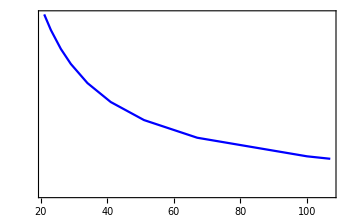
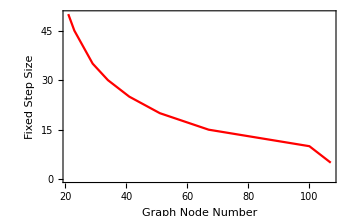
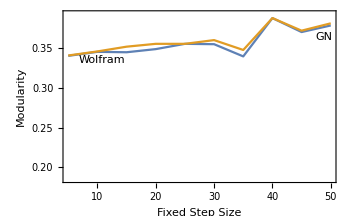
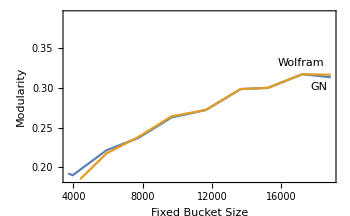

```mathematica
tickvalues={{0,0},{5000,5000},{10000,10000},{15000,15000}};
ticks=MapAt[Rotate[#,Pi/2]&,tickvalues,{All,-1}];
{Overlay[{ListLinePlot[Thread[{nodenumbers,bucketamounts}],Frame->True,ImagePadding->35,FrameTicks->{{None,ticks},{All,None}},FrameLabel->{{None,Style["Fixed Bucket Size",Blue]},{None,None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}],ListLinePlot[Thread[{nodenumbers,stepamounts}],Frame->True,ImagePadding->35,FrameTicks->{{All,None},{All,None}},FrameLabel->{"Graph Node Number",Style["Fixed Step Size",Red]},PlotStyle->Red,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}]}],ListLinePlot[{Thread[{stepamounts,GNmodularityvalues}],Thread[{stepamounts,modularityvalues}]},Frame->True,FrameLabel->{"Fixed Step Size","Modularity"},ImageSize->350,PlotRange->{{First@stepamounts,Last@stepamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}},PlotLabels->Placed[{"GN","Wolfram"},{Scaled[1],Below}]](*,ListLinePlot[Thread[{Range[5,50,5],modularityvalues}],Frame->True,FrameLabel->{"Fixed Step Size","Modularity (Wolfram)"},ImageSize->350,PlotRange->Automatic]*),ListLinePlot[{Thread[{bucketamounts,GNmodularityvaluesFixedbucket}],Thread[{bucketamounts,modularityvaluesFixedbucket}]},Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity"},ImageSize->350,PlotRange->{{First@bucketamounts,Last@bucketamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}},PlotLabels->Placed[{"GN","Wolfram"},{Scaled[1],Above}]](*,ListLinePlot[Thread[{graphsandnodenumbers[[All,2]],modularityvaluesFixedbucket}],Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity (Wolfram)"},ImageSize->350,PlotRange->Automatic]*)}
```

```mathematica
AbsoluteTiming[thicknessdatavaryingFixedstep=Table[snetworkdatabinned[10,i,"datafull"],{i,Range@10}];]
graphsandnodenumbers=Table[snetworkgraph[thicknessdatavaryingFixedstep[[i]][[1]],thicknessdatavaryingFixedstep[[i]][[2]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
```

{93.5853,Null}

```mathematica
AbsoluteTiming[thicknessdatavaryingFixedbucket=Table[snetworkdatafxdbucket[10,i,"datafull"],{i,graphsandnodenumbers[[All,2]]}];]
graphsandnodenumbersFixedbucket=Table[snetworkgraph[thicknessdatavaryingFixedbucket[[i]][[1]],thicknessdatavaryingFixedbucket[[i]][[2]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
GNmodularityvaluesFixedbucket=Table[GirvanNewmanmodularity[graphsandnodenumbersFixedbucket[[i]][[1]]],{i,Length@graphsandnodenumbersFixedbucket}];
modularityvaluesFixedbucket=Table[N@GraphAssortativity[graphsandnodenumbersFixedbucket[[i]][[1]],FindGraphCommunities[graphsandnodenumbersFixedbucket[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbersFixedbucket}];
```

{818.97,Null}

```mathematica
stepamounts=Range@10
nodenumbers=graphsandnodenumbers[[All,2]]
bucketamounts=Table[(Values@Counts@thicknessdatavaryingFixedbucket[[i,1]])[[1]],{i,10}]
```

{1,2,3,4,5,6,7,8,9,10}

{35,19,14,11,9,8,7,6,6,5}

{11284,20832,28287,36006,44008,49512,56580,66016,66016,79216}

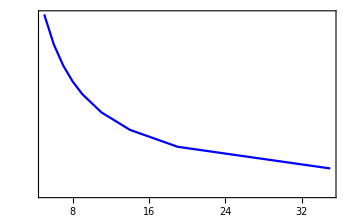
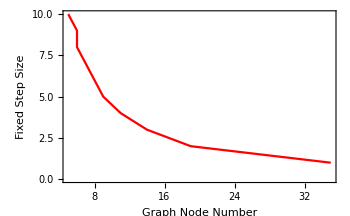
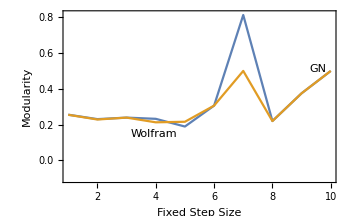
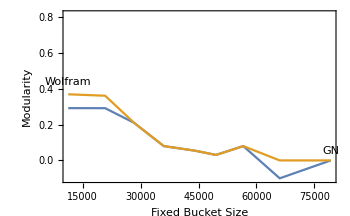

```mathematica
tickvalues={{0,0},{20000,20000},{40000,40000},{60000,60000},{80000,80000}};
ticks=MapAt[Rotate[#,Pi/2]&,tickvalues,{All,-1}];
{Overlay[{ListLinePlot[Thread[{nodenumbers,bucketamounts}],Frame->True,ImagePadding->35,FrameTicks->{{None,ticks},{All,None}},FrameLabel->{{None,Style["Fixed Bucket Size",Blue]},{None,None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}],ListLinePlot[Thread[{nodenumbers,stepamounts}],Frame->True,ImagePadding->35,FrameTicks->{{All,None},{All,None}},FrameLabel->{"Graph Node Number",Style["Fixed Step Size",Red]},PlotStyle->Red,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}]}],ListLinePlot[{Thread[{stepamounts,GNmodularityvalues}],Thread[{stepamounts,modularityvalues}]},Frame->True,FrameLabel->{"Fixed Step Size","Modularity"},ImageSize->350,PlotRange->{{First@stepamounts,Last@stepamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}},PlotLabels->Placed[{"GN","Wolfram"},{Scaled[1],Below}]],ListLinePlot[{Thread[{bucketamounts,GNmodularityvaluesFixedbucket}],Thread[{bucketamounts,modularityvaluesFixedbucket}]},Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity"},ImageSize->350,PlotRange->{{First@bucketamounts,Last@bucketamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}},PlotLabels->Placed[{"GN","Wolfram"},{Scaled[1],Above}]]}
```

```mathematica
AbsoluteTiming[lengthdatavaryingFixedstep=Table[snetworkdatabinned[12,i,"datafull"],{i,Range[400,4000,400]}];]
graphsandnodenumbers=Table[snetworkgraph[lengthdatavaryingFixedstep[[i]][[1]],lengthdatavaryingFixedstep[[i]][[2]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
```

{186.879,Null}

```mathematica
AbsoluteTiming[lengthdatavaryingFixedbucket=Table[snetworkdatafxdbucket[12,i,"datafull"],{i,graphsandnodenumbers[[All,2]]}];]
graphsandnodenumbersFixedbucket=Table[snetworkgraph[lengthdatavaryingFixedbucket[[i]][[1]],lengthdatavaryingFixedbucket[[i]][[2]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
GNmodularityvaluesFixedbucket=Table[GirvanNewmanmodularity[graphsandnodenumbersFixedbucket[[i]][[1]]],{i,Length@graphsandnodenumbersFixedbucket}];
modularityvaluesFixedbucket=Table[N@GraphAssortativity[graphsandnodenumbersFixedbucket[[i]][[1]],FindGraphCommunities[graphsandnodenumbersFixedbucket[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbersFixedbucket}];
```

{89.5098,Null}

```mathematica
stepamounts=Range[400,4000,400]
nodenumbers=graphsandnodenumbers[[All,2]]
bucketamounts=Table[(Values@Counts@lengthdatavaryingFixedbucket[[i,1]])[[1]],{i,10}]
```

{400,800,1200,1600,2000,2400,2800,3200,3600,4000}

{102,54,36,28,22,20,17,16,13,12}

{3884,7336,11003,14147,18005,19805,23300,24756,30469,33008}

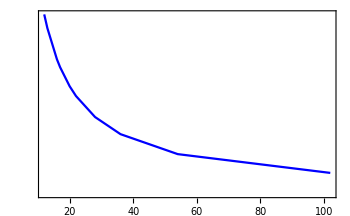
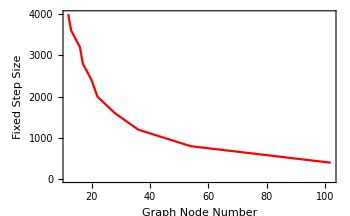
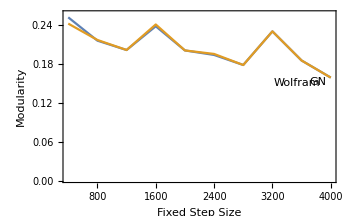
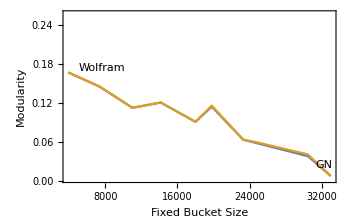

```mathematica
tickvalues={{0,0},{7000,7000},{14000,14000},{21000,21000},{28000,28000},{35000,35000}};
ticks=MapAt[Rotate[#,Pi/2]&,tickvalues,{All,-1}];
tickvaluesst={{0,0},{1000,1000},{2000,2000},{3000,3000},{4000,4000}};
ticksst=MapAt[Rotate[#,Pi/2]&,tickvaluesst,{All,-1}];
{Overlay[{ListLinePlot[Thread[{nodenumbers,bucketamounts}],Frame->True,ImagePadding->35,FrameTicks->{{None,ticks},{All,None}},FrameLabel->{{None,Style["Fixed Bucket Size",Blue]},{None,None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}],ListLinePlot[Thread[{nodenumbers,stepamounts}],Frame->True,ImagePadding->35,FrameTicks->{{ticksst,None},{All,None}},FrameLabel->{"Graph Node Number",Style["Fixed Step Size",Red]},PlotStyle->Red,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}]}],ListLinePlot[{Thread[{stepamounts,GNmodularityvalues}],Thread[{stepamounts,modularityvalues}]},Frame->True,FrameLabel->{"Fixed Step Size","Modularity"},ImageSize->350,PlotRange->{{First@stepamounts,Last@stepamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}},PlotLabels->Placed[{"GN","Wolfram"},{Scaled[1],Below}]],ListLinePlot[{Thread[{bucketamounts,GNmodularityvaluesFixedbucket}],Thread[{bucketamounts,modularityvaluesFixedbucket}]},Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity"},ImageSize->350,PlotRange->{{First@bucketamounts,Last@bucketamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}},PlotLabels->Placed[{"GN","Wolfram"},{Scaled[1],Above}]]}
```

```mathematica
AbsoluteTiming[weightdatavaryingFixedstep=Table[snetworkdatabinned[11,i,"datafull"],{i,Range[200,2000,200]}];]
graphsandnodenumbers=Table[snetworkgraph[weightdatavaryingFixedstep[[i]][[1]],weightdatavaryingFixedstep[[i]][[2]],2,7,400,Red],{i,Range@10}];
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
```

{227.761,Null}

```mathematica
AbsoluteTiming[weightdatavaryingFixedbucket=Table[snetworkdatafxdbucket[12,i,"datafull"],{i,graphsandnodenumbers[[All,2]]}];]
graphsandnodenumbersFixedbucket=Table[snetworkgraph[weightdatavaryingFixedbucket[[i]][[1]],weightdatavaryingFixedbucket[[i]][[2]],2,7,400,Red],{i,Range@10}];
GNmodularityvaluesFixedbucket=Table[GirvanNewmanmodularity[graphsandnodenumbersFixedbucket[[i]][[1]]],{i,Length@graphsandnodenumbersFixedbucket}];
modularityvaluesFixedbucket=Table[N@GraphAssortativity[graphsandnodenumbersFixedbucket[[i]][[1]],FindGraphCommunities[graphsandnodenumbersFixedbucket[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbersFixedbucket}];
```

{91.914,Null}

```mathematica
stepamounts=Range[200,2000,200]
nodenumbers=graphsandnodenumbers[[All,2]]
bucketamounts=Table[(Values@Counts@weightdatavaryingFixedbucket[[i,1]])[[1]],{i,10}]
```

{200,400,600,800,1000,1200,1400,1600,1800,2000}

{110,56,38,29,23,19,18,15,14,12}

{3601,7074,10424,13659,17222,20848,22006,26407,28293,33008}

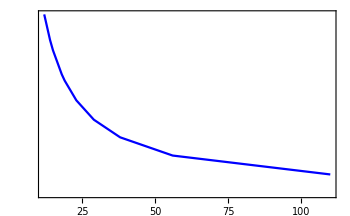
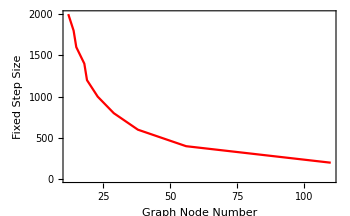
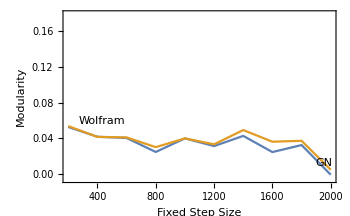
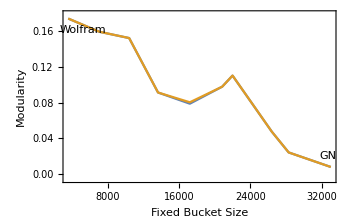

```mathematica
tickvalues={{0,0},{7000,7000},{14000,14000},{21000,21000},{28000,28000},{35000,35000}};
ticks=MapAt[Rotate[#,Pi/2]&,tickvalues,{All,-1}];
tickvaluesst={{0,0},{500,500},{1000,1000},{1500,1500},{2000,2000}};
ticksst=MapAt[Rotate[#,Pi/2]&,tickvaluesst,{All,-1}];
{Overlay[{ListLinePlot[Thread[{nodenumbers,bucketamounts}],Frame->True,ImagePadding->35,FrameTicks->{{None,ticks},{All,None}},FrameLabel->{{None,Style["Fixed Bucket Size",Blue]},{None,None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}],ListLinePlot[Thread[{nodenumbers,stepamounts}],Frame->True,ImagePadding->35,FrameTicks->{{ticksst,None},{All,None}},FrameLabel->{"Graph Node Number",Style["Fixed Step Size",Red]},PlotStyle->Red,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}]}],ListLinePlot[{Thread[{stepamounts,GNmodularityvalues}],Thread[{stepamounts,modularityvalues}]},Frame->True,FrameLabel->{"Fixed Step Size","Modularity"},ImageSize->350,PlotRange->{{First@stepamounts,Last@stepamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}},PlotLabels->Placed[{"GN","Wolfram"},{Scaled[1],Above}]],ListLinePlot[{Thread[{bucketamounts,GNmodularityvaluesFixedbucket}],Thread[{bucketamounts,modularityvaluesFixedbucket}]},Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity"},ImageSize->350,PlotRange->{{First@bucketamounts,Last@bucketamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}},PlotLabels->Placed[{"GN","Wolfram"},{Scaled[1],Top}]]}
```

Width Graphs for Varying Fixed Step Sizes and Fixed Bucket Sizes

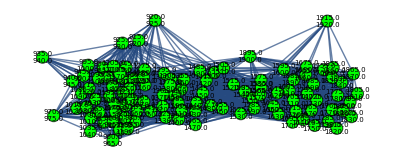
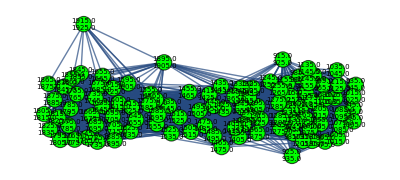
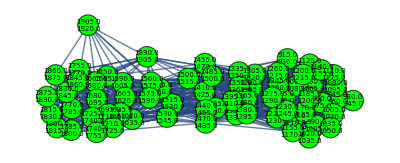
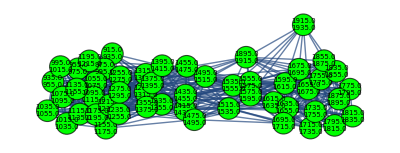
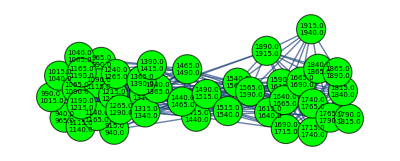
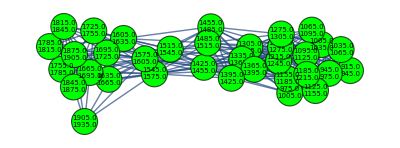
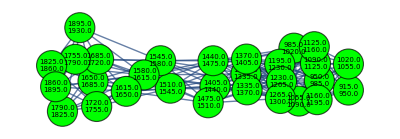
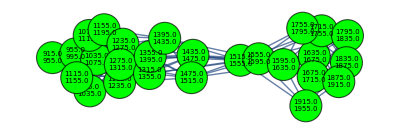
{{-Graphics-,107},{-Graphics-,100},{-Graphics-,67},{-Graphics-,51},{-Graphics-,41},{-Graphics-,34},{-Graphics-,29},{-Graphics-,26},{-Graphics-,23},{-Graphics-,21}}

```mathematica
graphsandnodenumbers
```

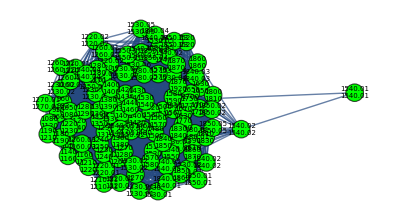
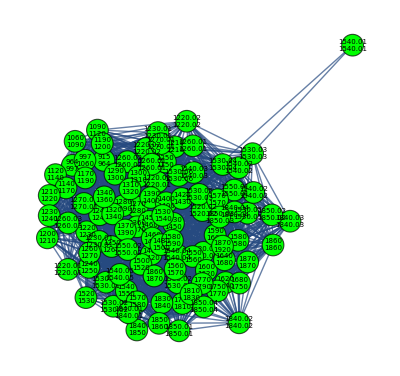
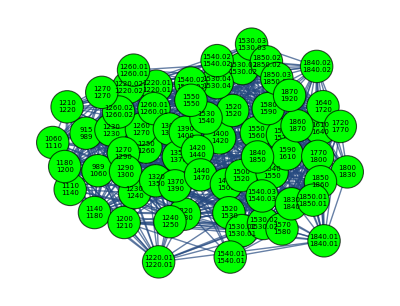
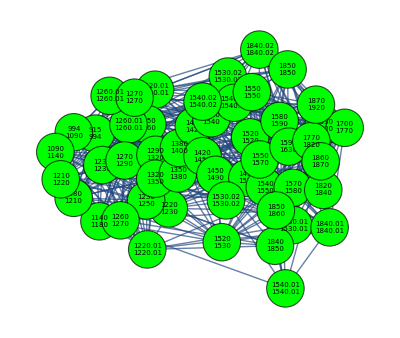
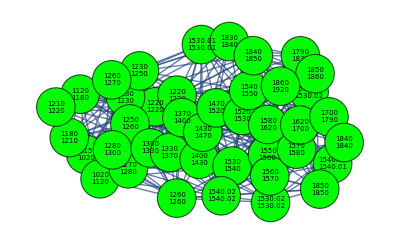
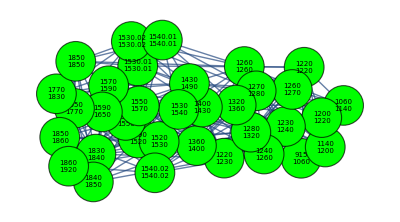
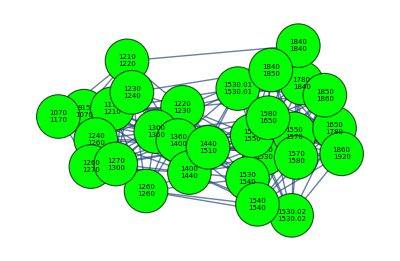
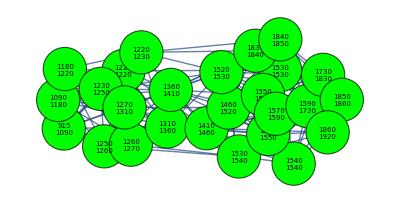
{{-Graphics-,107},{-Graphics-,100},{-Graphics-,67},{-Graphics-,51},{-Graphics-,41},{-Graphics-,34},{-Graphics-,29},{-Graphics-,26},{-Graphics-,23},{-Graphics-,21}}

```mathematica
graphsandnodenumbersFixedbucket
```

Thickness Graphs for Varying Fixed Step Sizes and Fixed Bucket Sizes

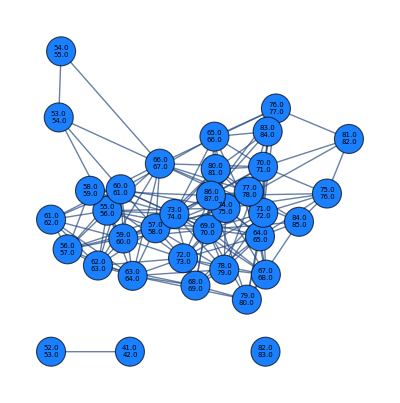
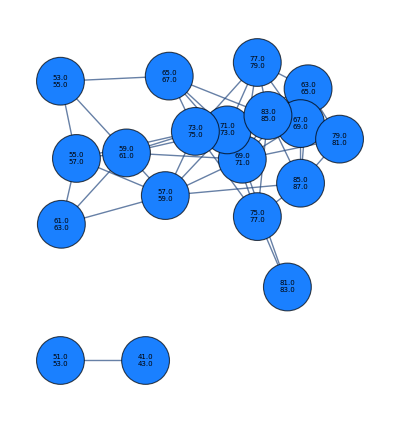
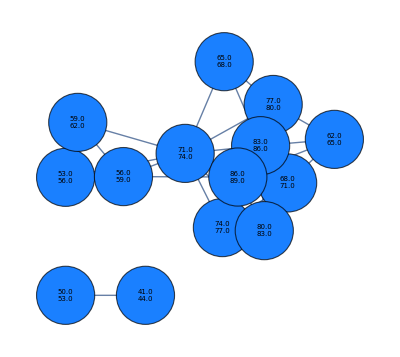
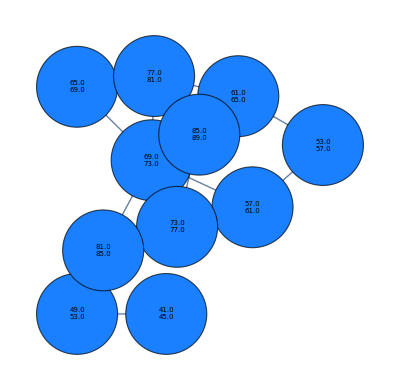
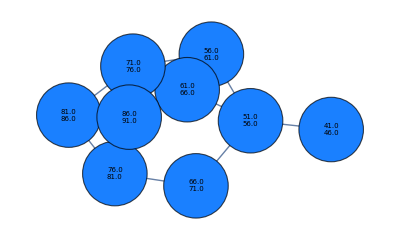
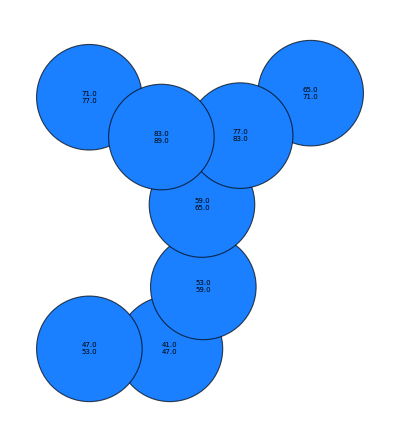
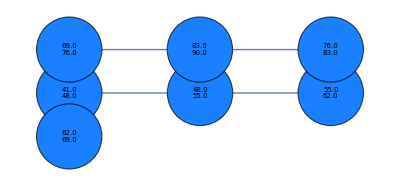
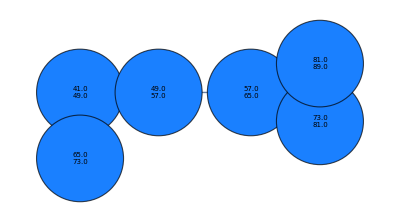
{{-Graphics-,35},{-Graphics-,19},{-Graphics-,14},{-Graphics-,11},{-Graphics-,9},{-Graphics-,8},{-Graphics-,7},{-Graphics-,6},{-Graphics-,6},{-Graphics-,5}}

```mathematica
graphsandnodenumbers
```

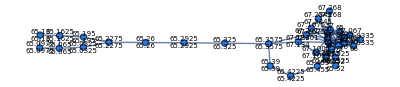
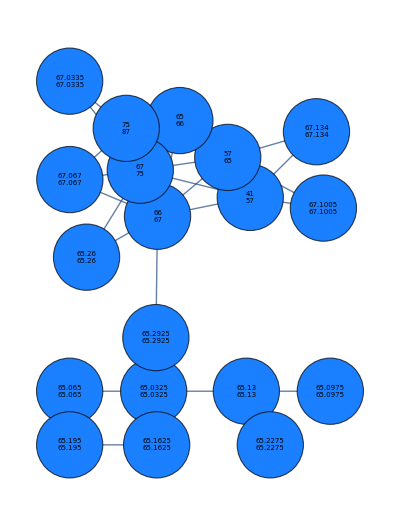
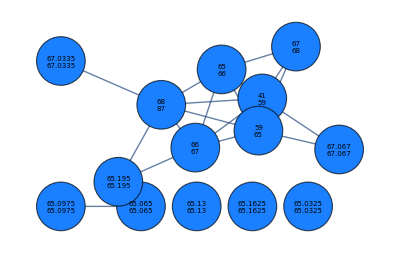
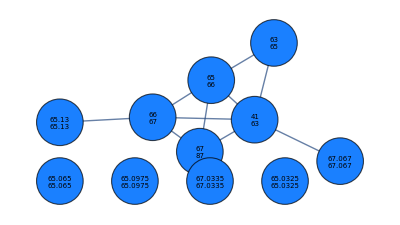
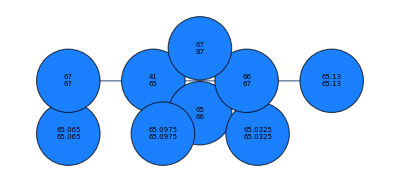
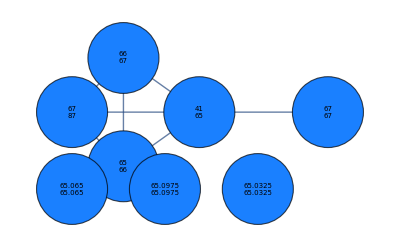
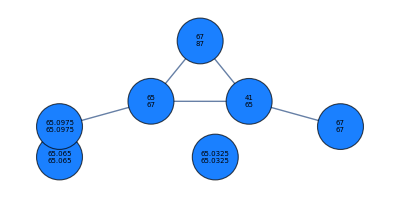
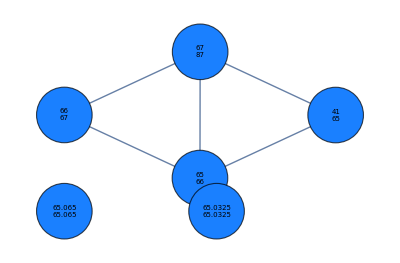
{{-Graphics-,35},{-Graphics-,19},{-Graphics-,14},{-Graphics-,11},{-Graphics-,9},{-Graphics-,8},{-Graphics-,7},{-Graphics-,6},{-Graphics-,6},{-Graphics-,5}}

```mathematica
graphsandnodenumbersFixedbucket
```

Length Graphs for Varying Fixed Step Sizes and Fixed Bucket Sizes

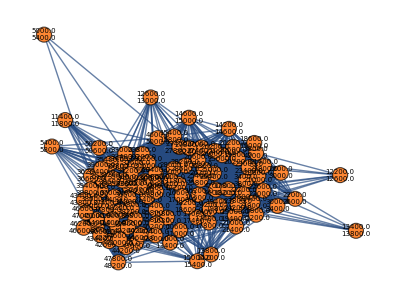
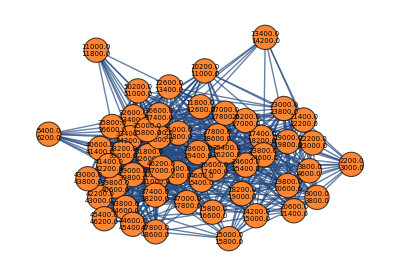
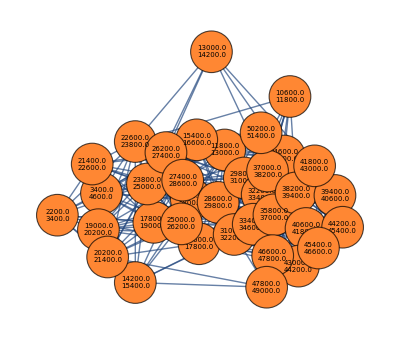
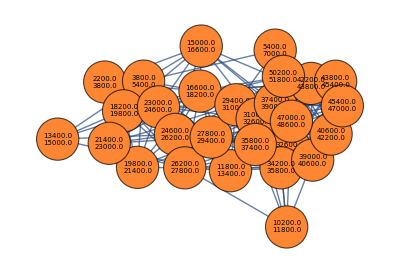
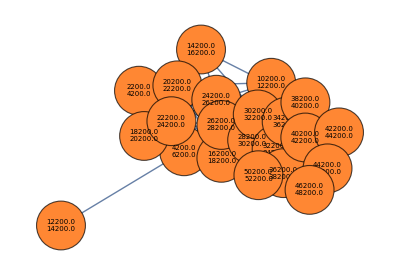
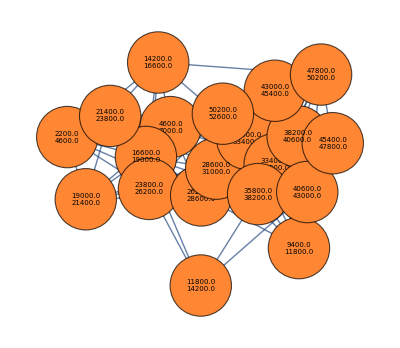
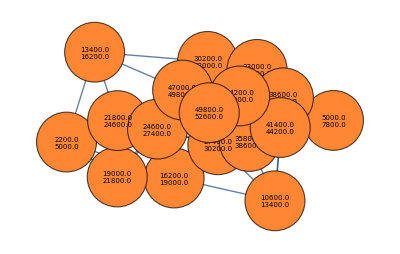
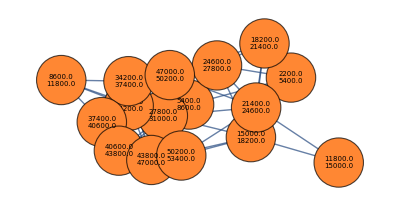
{{-Graphics-,102},{-Graphics-,54},{-Graphics-,36},{-Graphics-,28},{-Graphics-,22},{-Graphics-,20},{-Graphics-,17},{-Graphics-,16},{-Graphics-,13},{-Graphics-,12}}

```mathematica
graphsandnodenumbers
```

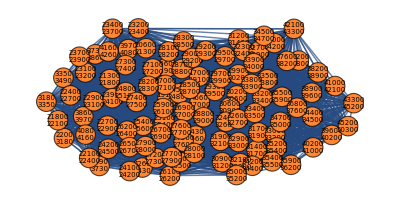
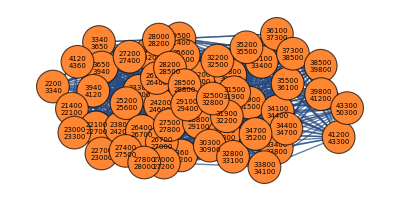
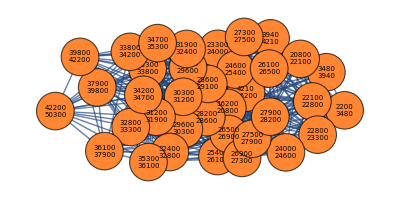
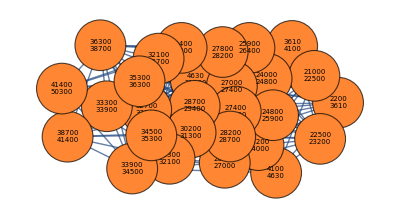
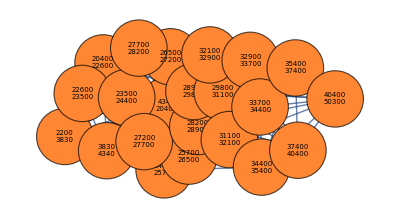
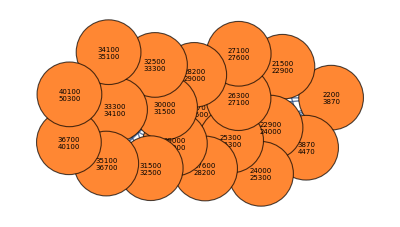
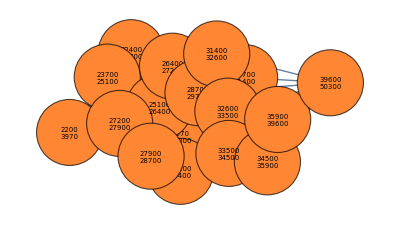
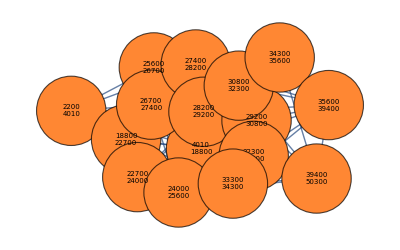
{{-Graphics-,102},{-Graphics-,54},{-Graphics-,36},{-Graphics-,28},{-Graphics-,22},{-Graphics-,20},{-Graphics-,17},{-Graphics-,16},{-Graphics-,13},{-Graphics-,12}}

```mathematica
graphsandnodenumbersFixedbucket
```

Weight Graphs for Varying Fixed Step Sizes and Fixed Bucket Sizes

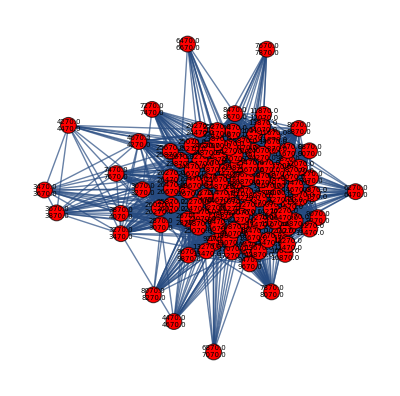
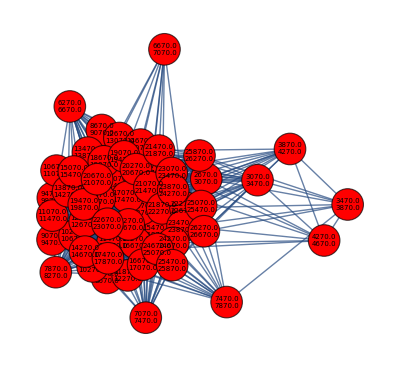
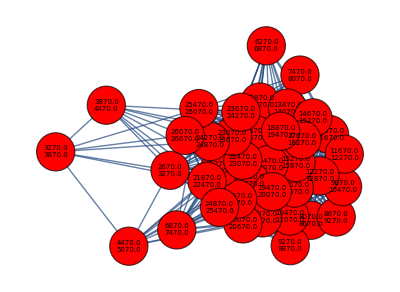
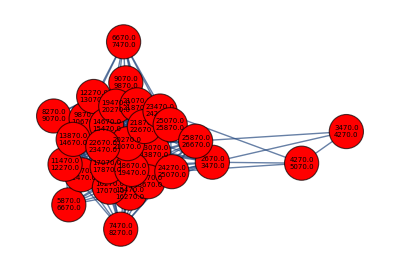
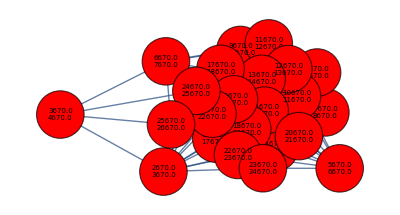
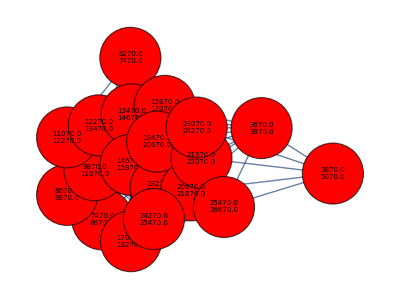
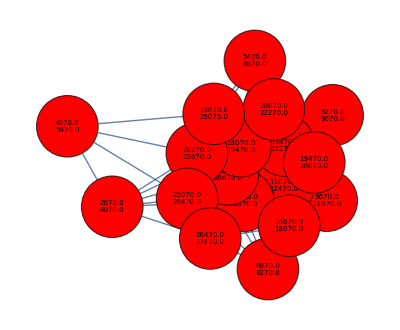
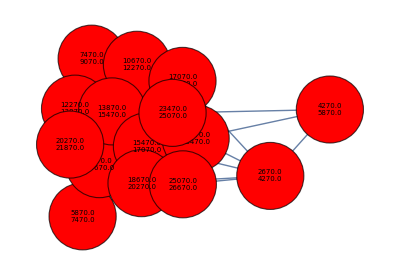
{{-Graphics-,110},{-Graphics-,56},{-Graphics-,38},{-Graphics-,29},{-Graphics-,23},{-Graphics-,19},{-Graphics-,18},{-Graphics-,15},{-Graphics-,14},{-Graphics-,12}}

```mathematica
graphsandnodenumbers
```

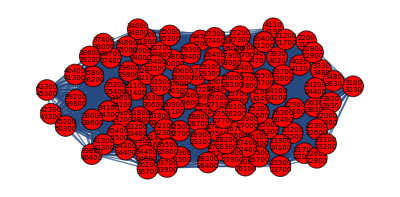
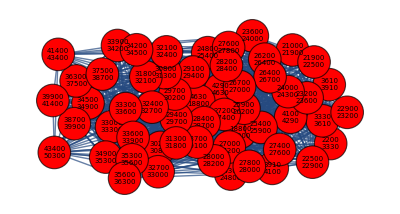
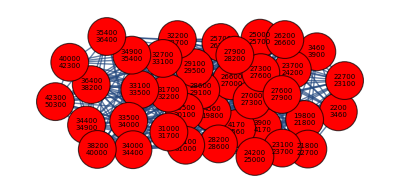
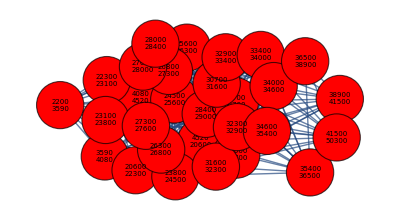
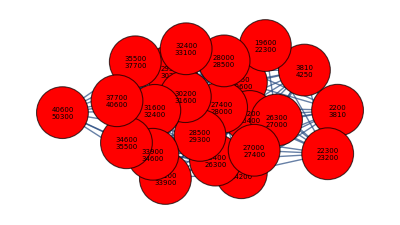
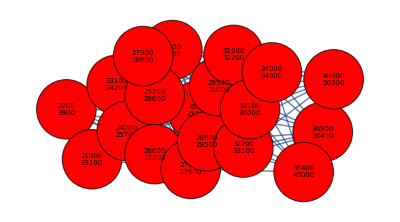
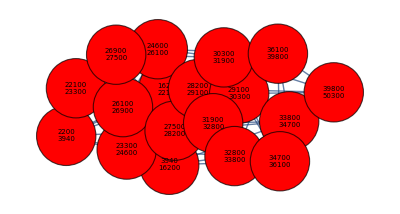
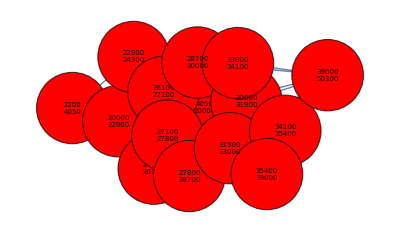
{{-Graphics-,110},{-Graphics-,56},{-Graphics-,38},{-Graphics-,29},{-Graphics-,23},{-Graphics-,19},{-Graphics-,18},{-Graphics-,15},{-Graphics-,14},{-Graphics-,12}}

```mathematica
graphsandnodenumbersFixedbucket
```

Plots Together

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,11,10];]
```

{48.4787,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

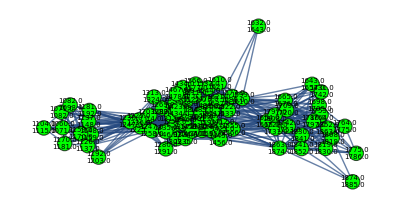
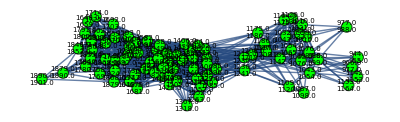
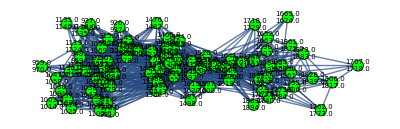
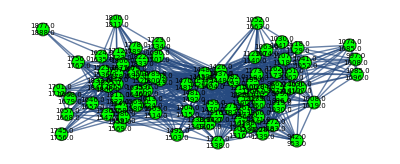
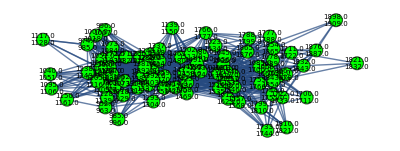
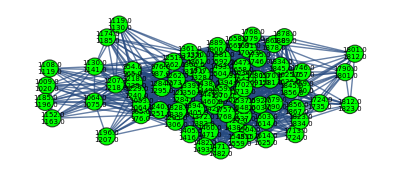
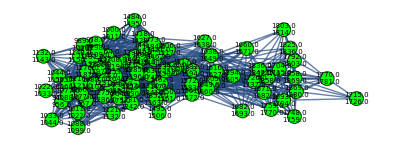
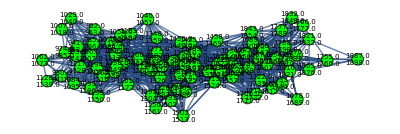
{{-Graphics-,71},{-Graphics-,85},{-Graphics-,88},{-Graphics-,83},{-Graphics-,83},{-Graphics-,76},{-Graphics-,81},{-Graphics-,86},{-Graphics-,85},{-Graphics-,87}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{244.235,{{33.57,40.9554,-19.8872},{40.4218,47.9585,-50.5403},{39.0145,45.3088,-56.4996},{43.6673,49.1992,-28.4451},{41.7119,47.7857,-37.8848},{22.2202,28.5683,-63.0805},{35.7747,41.8342,-58.0281},{39.7642,47.8633,-39.7476},{52.156,60.1734,-34.2295},{55.885,59.8185,-23.5193}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,3,2,2,3,2,2,2}

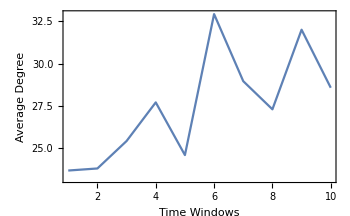
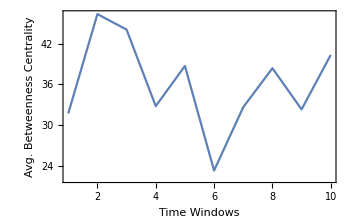
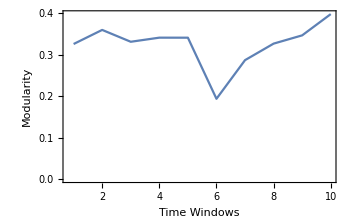
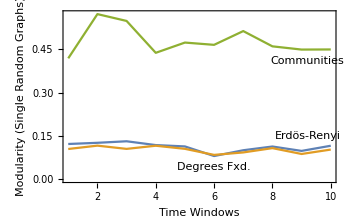
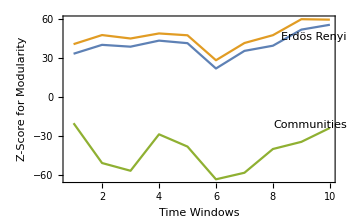

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[10,1,10];]
```

{13.7807,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep[[1]][[i]],thicknessdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

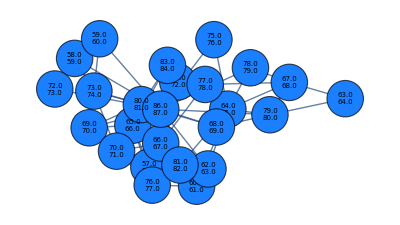
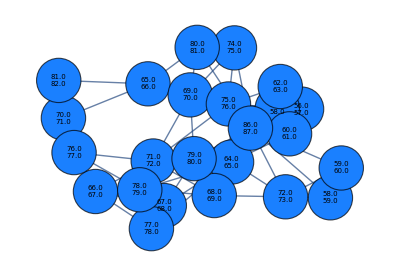
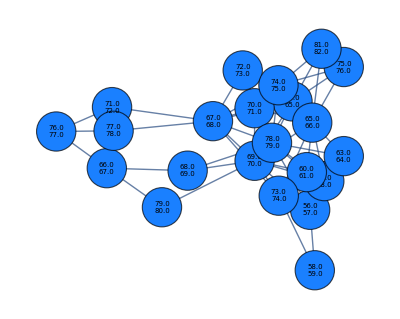
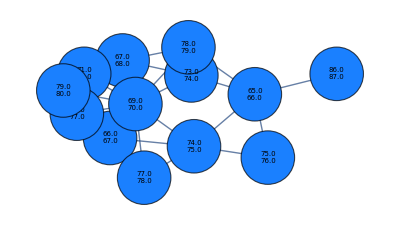
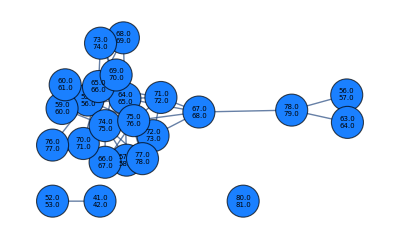
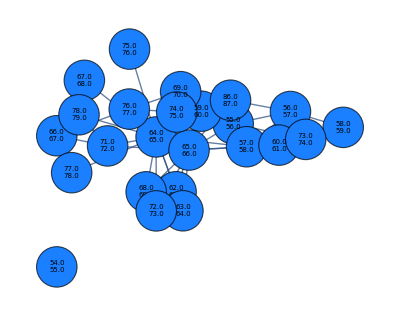
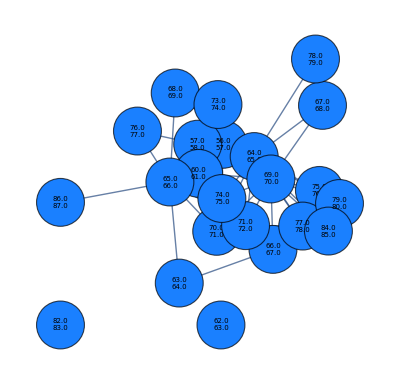
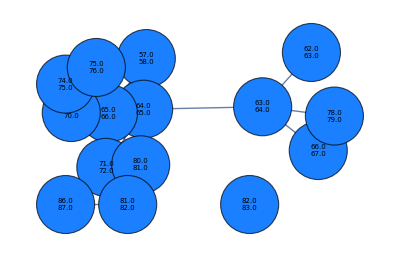
{{-Graphics-,25},{-Graphics-,24},{-Graphics-,22},{-Graphics-,13},{-Graphics-,24},{-Graphics-,24},{-Graphics-,23},{-Graphics-,15},{-Graphics-,12},{-Graphics-,12}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{93.2888,{{2.50502,4.54607,-6.06845},{4.11302,5.20171,-6.38714},{4.3782,6.11277,-4.85},{0.716177,1.36241,-3.21859},{0.134648,ComplexInfinity,-4.1646},{1},{-0.474878,ComplexInfinity,-6.80042},{0.585053,ComplexInfinity,(30 √1110 (0.34814+1/1000))/(√1)},{-0.897705,0.446371,-3.28261},{1.67402,1.84314,-1.75217}}}
 |  |  |  |

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{4,4,3,3,5,5,5,4,2,3}

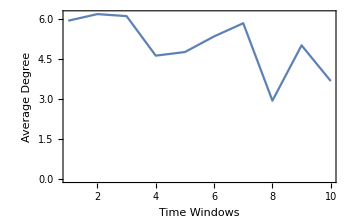
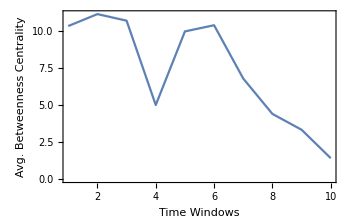
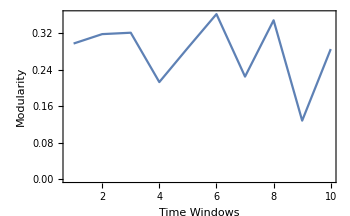
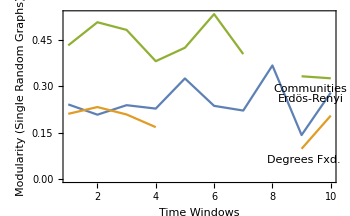
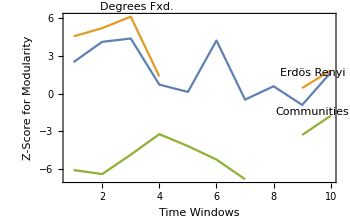

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[12,400,10];]
```

{61.2188,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedstep[[1]][[i]],lengthdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
```

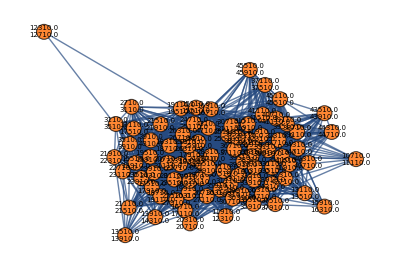
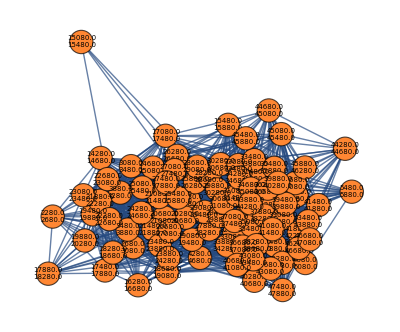
{{-Graphics-,84},{-Graphics-,89},{-Graphics-,79},{-Graphics-,87},{-Graphics-,90},{-Graphics-,77},{-Graphics-,83},{-Graphics-,83},{-Graphics-,85},{-Graphics-,86}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{530.131,{{35.7081,45.2461,-78.1516},{41.6224,48.2656,-78.9717},{33.8486,37.5899,-75.6403},{48.8782,55.501,-79.2671},{39.6166,47.0115,-76.2427},{24.1346,30.4739,-84.9721},{24.3581,29.614,-107.266},{30.2289,35.8713,-71.9001},{33.6259,36.8646,-79.0163},{35.8483,40.8516,-73.0956}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,3,2}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[11,200,10];]
```

{77.0267,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedstep[[1]][[i]],weightdataintimewindowsFixedstep[[2]][[i]],2,7,400,Red],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,94},{-Graphics-,90},{-Graphics-,89},{-Graphics-,97},{-Graphics-,91},{-Graphics-,92},{-Graphics-,96},{-Graphics-,89},{-Graphics-,100},{-Graphics-,95}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{674.48,{{7.62639,14.3356,-82.984},{1.14625,5.60766,-109.218},{3.50924,7.04036,-114.502},{8.94567,14.6903,-120.16},{7.66123,14.1205,-99.8434},{12.782,18.6146,-111.619},{7.75521,10.747,-138.651},{3.42677,6.94266,-80.2143},{3.2996,7.69011,-94.6969},{8.27245,12.244,-117.493}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,3,3,2,3,3,3,3}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{All,{0,20}},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{All,{-150,0}},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[9,85,10];]
```

{5.36296,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket[[1]][[i]],widthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Green],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{281.521,{{18.1208,22.7519,-65.7198},{18.4316,23.9744,-50.6182},{21.7818,24.2696,-53.3967},{36.0531,40.7257,-44.7595},{26.9589,33.176,-48.7689},{12.3565,16.4717,-82.235},{19.0099,25.0379,-63.0921},{32.3239,37.1309,-45.9318},{22.5486,32.0465,-62.4136},{50.035,55.7312,-34.7445}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,3,2,2,2,3,3,2,3,3}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[10,20,10];]
```

{5.16073,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket[[1]][[i]],thicknessdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{65.1567,{{4.07445,5.50428,-4.0838},{2.68955,4.14274,-5.86804},{1.83862,2.54654,-3.07004},{5.26397,4.6218,-0.125558},{3.0181,4.33807,-3.21577},{0.924623,1.94833,-3.23749},{0.213684,0.962007,-2.55683},{1.64527,2.95783,-1.56844},{4.68317,5.01019,1.85761},{4.64162,4.59406,1.34961}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,3,3,3,3,3,4,4}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[12,102,10];]
```

{6.6219,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedbucket[[1]][[i]],lengthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{1229.7,{{18.9852,19.9745,-163.711},{46.3861,53.5962,-133.914},{60.6419,63.9224,-116.304},{59.2833,63.7099,-108.884},{53.4703,56.04,-114.006},{30.6836,31.0555,-151.224},{27.8457,32.9705,-158.79},{41.9923,47.0041,-103.988},{47.0245,51.2727,-117.141},{43.1295,49.4626,-123.508}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,3,2,3,2,2,2}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[11,100,10];]
```

{6.95992,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedbucket[[1]][[i]],weightdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Red],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{855.782,{{34.8401,39.9894,-123.48},{28.4128,32.2426,-120.603},{22.9095,26.2783,-152.214},{17.1835,18.729,-139.01},{18.5607,18.9559,-145.308},{26.775,28.4406,-127.48},{11.8857,13.5977,-158.882},{31.1421,37.6489,-76.5715},{9.14574,11.3237,-119.686},{15.8447,19.4654,-128.804}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,3,3,3,3,3,2}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Plots for Network Metrics and Z-scores

Modeling Works with OR Methods

FBA Model Reproducing from Kauffman et al. 2003

```mathematica
stochmatrix={{-1,-1,1,0,1,0,0},{1,0,0,1,0,-1,0},{0,1,-1,-1,0,0,-1}};
objectivefunc1={2,0,0,1,0,0,0};
objectivefunc2={1,0,0,2,0,0,0};
boundaries={{0,Infinity},{0,Infinity},{0,0},{0,Infinity},{0,1},{0,2},{0,0}};
steadystatevector={{0,0},{0,0},{0,0}};
Vvector={v1,v2,v3,v4,b1,b2,b3};
```

stochmatrix . Vvector = steadystatevector  ,   -objectivefunc ∈ solution space within boundaries
A, B, and C are metabolites. , , , and  are reactions. , , and  are flux exchanges.

```mathematica
Print["1st objective function solution vector: ",Vvector1=LinearProgramming[-objectivefunc1,stochmatrix,steadystatevector,boundaries]]
Print["2nd objective function solution vector: ",Vvector2=LinearProgramming[-objectivefunc2,stochmatrix,steadystatevector,boundaries]]
```

1st objective function solution vector: {1,0,0,0,1,1,0}

2nd objective function solution vector: {0,1,0,1,1,1,0}

```mathematica
Show[RegionPlot[0<+<2,{,0,2},{,0,2},Frame->True,PlotLabels->Placed["0<+<2",{0.8,0.5}],FrameLabel->{"",""}],Plot[-+2,{,0,1.2},Frame->True,PlotLabels->Placed["+=2",{1.1,1}]],PlotRange->All,ImageSize->Small]
```

-Graphics-

```mathematica
FindMaximum[{v4+2v1,-v1-v2+v3+b1==0&&v1+v4-b2==0&&v2-v3-v4-b3==0&&0≤v1+v2≤1&&0≤v1+v4≤2&&v2-v4==0&&0≤b1≤1&&0≤b2≤2&&b3==0&&v1≥0&&v2≥0&&v3==0&&v4≥0},{v1,v2,v3,v4,b1,b2,b3}]
```

{2.,{v1→1.,v2→0.,v3→0.,v4→0.,b1→1.,b2→1.,b3→0.}}

```mathematica
AdjmatR=Transpose[stochmatrix].stochmatrix;
NormAdjmatR=AdjmatR/.x_/;x≠0->1;
AdjmatM=stochmatrix.Transpose[stochmatrix];
NormAdjmatM=AdjmatM/.x_/;x≠0->1;
```

```mathematica
{AdjacencyGraph[NormAdjmatR,{DirectedEdges->False,VertexSize->0.3,VertexStyle->Red,VertexLabels->{1->"v1",2->"v2",3->"v3",4->"v4",5->"b1",6->"b2",7->"b3"}}],AdjacencyGraph[NormAdjmatM,{DirectedEdges->False,VertexSize->0.3,VertexStyle->Red,VertexLabels->{1->"A",2->"B",3->"C"}}]}
```

{-Graphics-,-Graphics-}

Implementation Trials

```mathematica
stoichioforhomosapiens=Drop[Import["iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
SparseArray[…]
```

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=1008;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
SeedRandom[6];
boundaries=RandomChoice[{0.7,0.3}->{{0,500},{0,0}},fluxexchanges];
SeedRandom[5];
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}]
```

```mathematica
Dimensions@Solutionvectors
```

{200,1008}

```mathematica
nonzerocolumnsinsolutionvectorswithstoichioforhomosapiens=Position[Table[Count[Solutionvectors[[All,i]],x_/;x≠0.],{i,fluxexchanges}],objectivefunctionamount];
```

```mathematica
strial=stoichioforhomosapiens[[All,Flatten@nonzerocolumnsinsolutionvectorswithstoichioforhomosapiens]];
Dimensions@strial
```

{738,396}

```mathematica
stoichiometricmatrix=strial;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=396;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
SeedRandom[6];
boundaries=RandomChoice[{0.7,0.3}->{{0,500},{0,0}},fluxexchanges];
SeedRandom[5];
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}]
```

```mathematica
nonzerocolumnsinsolutionvectorswithstrial=Position[Table[Count[Solutionvectors[[All,i]],x_/;x≠0.],{i,fluxexchanges}],objectivefunctionamount];
```

```mathematica
Dimensions@nonzerocolumnsinsolutionvectorswithstrial
```

{116,1}

```mathematica
strial2=strial[[All,Flatten@nonzerocolumnsinsolutionvectorswithstrial]];
Dimensions@strial2
```

{738,116}

```mathematica
stoichiometricmatrix=strial2;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=116;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
SeedRandom[6];
boundaries=RandomChoice[{0.7,0.3}->{{0,500},{0,0}},fluxexchanges];
SeedRandom[5];
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}]
```

```mathematica
(* with 3rd trial, solution vectors resulted as zeros *)
```

```mathematica
nonzerocolumnsinsolutionvectorswithstrial2=Position[Table[Count[Solutionvectors[[All,i]],x_/;x≠0.],{i,fluxexchanges}],objectivefunctionamount];
nonzerocolumnsinsolutionvectorswithstrial2
```

{{22},{23},{25},{26},{39},{40},{51},{53},{54},{55},{56},{62},{63},{67},{73},{79},{81},{84},{85},{86},{87},{90},{91},{105},{108},{109}}

```mathematica
networkfeaturesdata=Solutionvectors[[All,Flatten@nonzerocolumnsinsolutionvectorswithstrial2]]*10^12;
```

```mathematica
{Histogram[Flatten@Solutionvectors,Frame->True,ScalingFunctions->"Log",PlotRange->All,FrameLabel->{"Flux Exchanges(inc. zero columns)","Counts"},ImageSize->450],Histogram[Flatten@networkfeaturesdata,Frame->True,PlotRange->All,FrameLabel->{"Flux Exchanges()","Counts"},ImageSize->450]}
```

{-Graphics-,-Graphics-}

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
data=networkfeaturesdata;
Dimensions@data
```

{200,26}

```mathematica
snetworkgraphsinglenodes[data[[]]]
```

```mathematica
(* snetworkgraphsinglenodes[aim_,campaign_,vertexsize_,vertexlabelsize_,imagesize_,vertexcolor_] *)
```